```mathematica
Clear["Global`*"]
```

```mathematica
name="/Users/tomoaki/BEM/fish/result.json"
imported=ImportString[StringReplace[Import[name,"text"],{"NaN"->"null","nan"->"null"}],"JSON"];
getData[var_,n_:0]:=If[n>0,(var/.imported)[[;;,n]],var/.imported];
```

/Users/tomoaki/BEM/fish/result.json

```mathematica
Column[imported[[;;,1]],Background->{{LightOrange,Orange}},Frame->True]
```

bodyA_COM
bodyA_EK
bodyA_EP
bodyA_accel
bodyA_area
bodyA_force
bodyA_pitch
bodyA_roll
bodyA_torque
bodyA_velocity
bodyA_yaw
bodyB_COM
bodyB_EK
bodyB_EP
bodyB_accel
bodyB_area
bodyB_force
bodyB_pitch
bodyB_roll
bodyB_torque
bodyB_velocity
bodyB_yaw
bodyC_COM
bodyC_EK
bodyC_EP
bodyC_accel
bodyC_area
bodyC_force
bodyC_pitch
bodyC_roll
bodyC_torque
bodyC_velocity
bodyC_yaw
time
water_E
water_EK
water_EP
water_volume

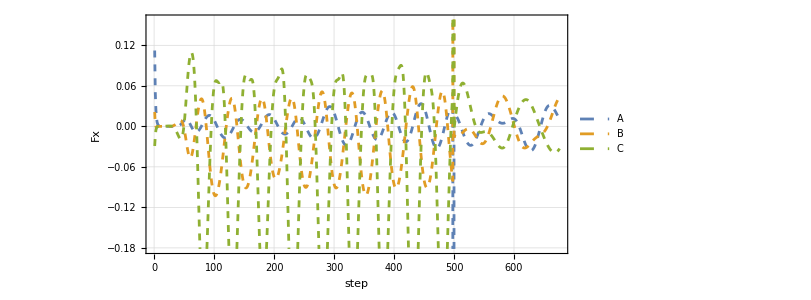

```mathematica
ListPlot[
{getData["bodyA_force",1],
getData["bodyB_force",1],
getData["bodyC_force",1]}
,Joined->True
,PlotStyle->{Dashed,Dashed,Dashed,Thick}
,PlotRange->Automatic
,BaseStyle->{FontFamily->"Times"}
,AspectRatio->1/2
,GridLines->Automatic
,Frame->True
,FrameLabel->{Style["step",FontSize->20,FontFamily->"Times",Italic],Style["Fx",FontSize->20,FontFamily->"Times",Italic]}
,FrameStyle->Directive[FontSize->20,Black,Thickness[0.002]],GridLines->{Table[i,{i,0.,4.,0.2}],Table[i,{i,-1.,1.,0.5}]},GridLinesStyle->Directive[Gray,Dotted]
,ImageSize->600
,PlotLegends->{"A","B","C"}
]
```

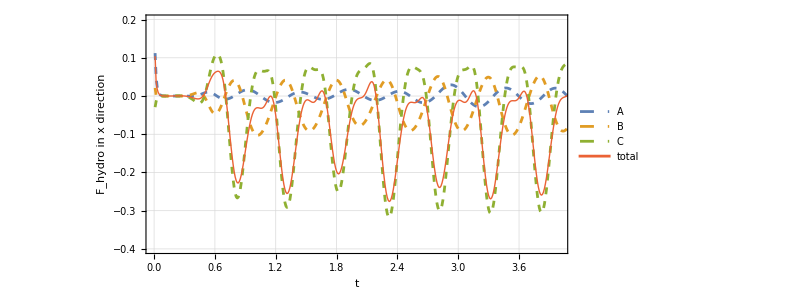

```mathematica
ListPlot[
{Transpose@{getData["time"],getData["bodyA_force",1]},
Transpose@{getData["time"],getData["bodyB_force",1]},
Transpose@{getData["time"],getData["bodyC_force",1]},
Transpose@{getData["time"],Total[Table[getData["body"<>a<>"_force",1],{a,{"A","B","C"}}]]}}
,Joined->True
,PlotStyle->{Dashed,Dashed,Dashed,Thick}
,PlotRange->{{0,4},{-0.4,0.2}}
,BaseStyle->{FontFamily->"Times"}
,AspectRatio->1/2
,GridLines->Automatic
,Frame->True
,FrameLabel->{Style["t",FontSize->20,FontFamily->"Times",Italic],Style["F_hydro in x direction",FontSize->20,FontFamily->"Times",Italic]}
,FrameStyle->Directive[FontSize->20,Black,Thickness[0.002]],GridLines->{Table[i,{i,0.,4.,0.2}],Table[i,{i,-1.,1.,0.5}]},GridLinesStyle->Directive[Gray,Dotted]
,ImageSize->600
,PlotLegends->{"A","B","C","total"}
]
```

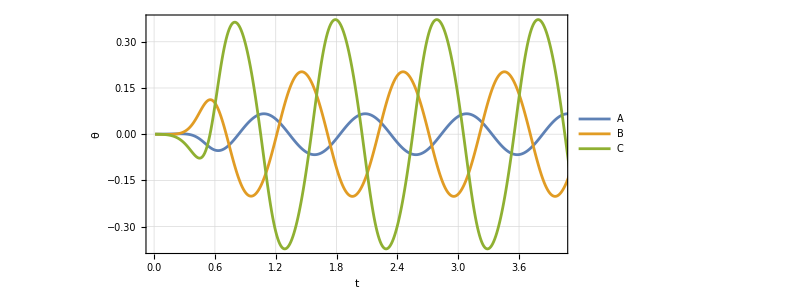

```mathematica
ListPlot[
{Transpose@{getData["time"],getData["bodyA_yaw"]},
Transpose@{getData["time"],getData["bodyB_yaw"]},
Transpose@{getData["time"],getData["bodyC_yaw"]}}
,Joined->True
,PlotRange->{{0,4},Automatic}
,BaseStyle->{FontFamily->"Times"}
,AspectRatio->1/2
,GridLines->Automatic
,Frame->True
,FrameLabel->{Style["t",FontSize->20,FontFamily->"Times",Italic],Style["θ",FontSize->20,FontFamily->"Times",Italic]}
,FrameStyle->Directive[FontSize->20,Black,Thickness[0.002]],GridLines->{Table[i,{i,0.,4.,0.2}],Table[i,{i,-1.,1.,0.5}]},GridLinesStyle->Directive[Gray,Dotted]
,ImageSize->600
,PlotLegends->{"A","B","C","total"}
]
```